```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
```

```mathematica
Ndof=1+n+n(n+1)/2//.{n->m+1,m->3}//FullSimplify
```

15

```mathematica
pc[T_,μB_]:=Sum[Subscript[a, 2i,2j] T^(2i)μB^(2j)KroneckerDelta[2(i+j),4],{i,0,2},{j,0,2}];
pnonc[T_,μB_]:=Sum[Subscript[b, i,2j] T^i μB^(2j),{i,0,4},{j,0,2}];
(*S[T_,μB_]:=1/2(1+Tanh[g(T^2+d μB^2-f)]);*)
p[T_,μB_]:=pc[T,μB]S[T,μB]+pnonc[T,μB](1-S[T,μB]);
s[T_,μB_]:=Evaluate[D[p[T,μB], T]];
ρB[T_,μB_]:=Evaluate[D[p[T,μB], μB]];
e[T_,μB_]:=T s[T,μB]+μB ρB[T,μB]-p[T,μB];
χTT[T_,μB_]:=Evaluate[D[p[T,μB], T,T]];
χTμB[T_,μB_]:=Evaluate[D[p[T,μB], T,μB]];
χμBμB[T_,μB_]:=Evaluate[D[p[T,μB], μB,μB]];
```

```mathematica
e[T,μB]//FullSimplify

p[T,μB]//FullSimplify
s[T,μB]//FullSimplify
ρB[T,μB]//FullSimplify
χTT[T,μB]//FullSimplify
χTμB[T,μB]//FullSimplify
χμBμB[T,μB]//FullSimplify
```

-b_(0,0)+μB^2 b_(0,2)+3 μB^4 b_(0,4)+2 T μB^2 b_(1,2)+4 T μB^4 b_(1,4)+T^2 b_(2,0)+3 T^2 μB^2 b_(2,2)+5 T^2 μB^4 b_(2,4)+2 T^3 b_(3,0)+4 T^3 μB^2 b_(3,2)+6 T^3 μB^4 b_(3,4)+3 T^4 b_(4,0)+5 T^4 μB^2 b_(4,2)+7 T^4 μB^4 b_(4,4)-S[T,μB] (-3 μB^4 a_(0,4)-3 T^2 μB^2 a_(2,2)-b_(0,0)+μB^2 b_(0,2)+3 μB^4 b_(0,4)+T (2 μB^2 (b_(1,2)+2 μB^2 b_(1,4))+T (b_(2,0)+3 μB^2 b_(2,2)+5 μB^4 b_(2,4)+T (-3 T a_(4,0)+2 b_(3,0)+3 T b_(4,0)+μB^2 (4 b_(3,2)+5 T b_(4,2)+μB^2 (6 b_(3,4)+7 T b_(4,4)))))))+μB (μB^4 a_(0,4)+T^2 μB^2 a_(2,2)+T^4 a_(4,0)) S^(0,1)[T,μB]-μB b_(0,0) S^(0,1)[T,μB]-μB (μB^2 b_(0,2)+μB^4 b_(0,4)+T (b_(1,0)+μB^2 b_(1,2)+μB^4 b_(1,4)+T (b_(2,0)+μB^2 b_(2,2)+μB^4 b_(2,4)+T (b_(3,0)+T b_(4,0)+μB^2 (b_(3,2)+T b_(4,2)+μB^2 (b_(3,4)+T b_(4,4))))))) S^(0,1)[T,μB]-T (-μB^4 a_(0,4)-T^2 μB^2 a_(2,2)+b_(0,0)+μB^2 b_(0,2)+μB^4 b_(0,4)+T (b_(1,0)+μB^2 b_(1,2)+μB^4 b_(1,4)+T (b_(2,0)+μB^2 b_(2,2)+μB^4 b_(2,4)+T (-T a_(4,0)+b_(3,0)+T b_(4,0)+μB^2 (b_(3,2)+T b_(4,2)+μB^2 (b_(3,4)+T b_(4,4))))))) S^(1,0)[T,μB]

S[T,μB] (μB^4 a_(0,4)+T^2 μB^2 a_(2,2)+T^4 a_(4,0))-(-1+S[T,μB]) (b_(0,0)+μB^2 b_(0,2)+μB^4 b_(0,4)+T (b_(1,0)+μB^2 b_(1,2)+μB^4 b_(1,4)+T (b_(2,0)+μB^2 b_(2,2)+μB^4 b_(2,4)+T (b_(3,0)+T b_(4,0)+μB^2 (b_(3,2)+T b_(4,2)+μB^2 (b_(3,4)+T b_(4,4)))))))

2 S[T,μB] (T μB^2 a_(2,2)+2 T^3 a_(4,0))-(-1+S[T,μB]) (b_(1,0)+μB^2 b_(1,2)+μB^4 b_(1,4)+T (2 b_(2,0)+2 μB^2 b_(2,2)+2 μB^4 b_(2,4)+T (3 b_(3,0)+3 μB^2 b_(3,2)+3 μB^4 b_(3,4)+4 T (b_(4,0)+μB^2 b_(4,2)+μB^4 b_(4,4)))))+(μB^4 a_(0,4)+T^2 μB^2 a_(2,2)+T^4 a_(4,0)) S^(1,0)[T,μB]-(b_(0,0)+μB^2 b_(0,2)+μB^4 b_(0,4)+T (b_(1,0)+μB^2 b_(1,2)+μB^4 b_(1,4)+T (b_(2,0)+μB^2 b_(2,2)+μB^4 b_(2,4)+T (b_(3,0)+T b_(4,0)+μB^2 (b_(3,2)+T b_(4,2)+μB^2 (b_(3,4)+T b_(4,4))))))) S^(1,0)[T,μB]

2 S[T,μB] (2 μB^3 a_(0,4)+T^2 μB a_(2,2))-2 μB (-1+S[T,μB]) (b_(0,2)+2 μB^2 b_(0,4)+T (b_(1,2)+2 μB^2 b_(1,4)+T (b_(2,2)+2 μB^2 b_(2,4)+T (b_(3,2)+T b_(4,2)+2 μB^2 (b_(3,4)+T b_(4,4))))))+(μB^4 a_(0,4)+T^2 μB^2 a_(2,2)+T^4 a_(4,0)) S^(0,1)[T,μB]-(b_(0,0)+μB^2 b_(0,2)+μB^4 b_(0,4)+T (b_(1,0)+μB^2 b_(1,2)+μB^4 b_(1,4)+T (b_(2,0)+μB^2 b_(2,2)+μB^4 b_(2,4)+T (b_(3,0)+T b_(4,0)+μB^2 (b_(3,2)+T b_(4,2)+μB^2 (b_(3,4)+T b_(4,4))))))) S^(0,1)[T,μB]

2 S[T,μB] (μB^2 a_(2,2)+6 T^2 a_(4,0))-2 (-1+S[T,μB]) (b_(2,0)+μB^2 b_(2,2)+μB^4 b_(2,4)+3 T (b_(3,0)+2 T b_(4,0)+μB^2 (b_(3,2)+2 T b_(4,2)+μB^2 (b_(3,4)+2 T b_(4,4)))))+4 (T μB^2 a_(2,2)+2 T^3 a_(4,0)) S^(1,0)[T,μB]-2 (b_(1,0)+μB^2 b_(1,2)+μB^4 b_(1,4)+T (2 b_(2,0)+2 μB^2 b_(2,2)+2 μB^4 b_(2,4)+T (3 b_(3,0)+3 μB^2 b_(3,2)+3 μB^4 b_(3,4)+4 T (b_(4,0)+μB^2 b_(4,2)+μB^4 b_(4,4))))) S^(1,0)[T,μB]+(μB^4 a_(0,4)+T^2 μB^2 a_(2,2)+T^4 a_(4,0)) S^(2,0)[T,μB]-(b_(0,0)+μB^2 b_(0,2)+μB^4 b_(0,4)+T (b_(1,0)+μB^2 b_(1,2)+μB^4 b_(1,4)+T (b_(2,0)+μB^2 b_(2,2)+μB^4 b_(2,4)+T (b_(3,0)+T b_(4,0)+μB^2 (b_(3,2)+T b_(4,2)+μB^2 (b_(3,4)+T b_(4,4))))))) S^(2,0)[T,μB]

4 T μB S[T,μB] a_(2,2)-2 μB (-1+S[T,μB]) (b_(1,2)+2 μB^2 b_(1,4)+T (2 b_(2,2)+4 μB^2 b_(2,4)+T (3 b_(3,2)+6 μB^2 b_(3,4)+4 T b_(4,2)+8 T μB^2 b_(4,4))))+2 (T μB^2 a_(2,2)+2 T^3 a_(4,0)) S^(0,1)[T,μB]-(b_(1,0)+μB^2 b_(1,2)+μB^4 b_(1,4)+T (2 b_(2,0)+2 μB^2 b_(2,2)+2 μB^4 b_(2,4)+T (3 b_(3,0)+3 μB^2 b_(3,2)+3 μB^4 b_(3,4)+4 T (b_(4,0)+μB^2 b_(4,2)+μB^4 b_(4,4))))) S^(0,1)[T,μB]+2 (2 μB^3 a_(0,4)+T^2 μB a_(2,2)) S^(1,0)[T,μB]-2 μB (b_(0,2)+2 μB^2 b_(0,4)+T (b_(1,2)+2 μB^2 b_(1,4)+T (b_(2,2)+2 μB^2 b_(2,4)+T (b_(3,2)+T b_(4,2)+2 μB^2 (b_(3,4)+T b_(4,4)))))) S^(1,0)[T,μB]+(μB^4 a_(0,4)+T^2 μB^2 a_(2,2)+T^4 a_(4,0)) S^(1,1)[T,μB]-(b_(0,0)+μB^2 b_(0,2)+μB^4 b_(0,4)+T (b_(1,0)+μB^2 b_(1,2)+μB^4 b_(1,4)+T (b_(2,0)+μB^2 b_(2,2)+μB^4 b_(2,4)+T (b_(3,0)+T b_(4,0)+μB^2 (b_(3,2)+T b_(4,2)+μB^2 (b_(3,4)+T b_(4,4))))))) S^(1,1)[T,μB]

2 S[T,μB] (6 μB^2 a_(0,4)+T^2 a_(2,2))-2 (-1+S[T,μB]) (b_(0,2)+6 μB^2 b_(0,4)+T (b_(1,2)+6 μB^2 b_(1,4)+T (b_(2,2)+6 μB^2 b_(2,4)+T (b_(3,2)+T b_(4,2)+6 μB^2 (b_(3,4)+T b_(4,4))))))+4 (2 μB^3 a_(0,4)+T^2 μB a_(2,2)) S^(0,1)[T,μB]-4 μB (b_(0,2)+2 μB^2 b_(0,4)+T (b_(1,2)+2 μB^2 b_(1,4)+T (b_(2,2)+2 μB^2 b_(2,4)+T (b_(3,2)+T b_(4,2)+2 μB^2 (b_(3,4)+T b_(4,4)))))) S^(0,1)[T,μB]+(μB^4 a_(0,4)+T^2 μB^2 a_(2,2)+T^4 a_(4,0)) S^(0,2)[T,μB]-(b_(0,0)+μB^2 b_(0,2)+μB^4 b_(0,4)+T (b_(1,0)+μB^2 b_(1,2)+μB^4 b_(1,4)+T (b_(2,0)+μB^2 b_(2,2)+μB^4 b_(2,4)+T (b_(3,0)+T b_(4,0)+μB^2 (b_(3,2)+T b_(4,2)+μB^2 (b_(3,4)+T b_(4,4))))))) S^(0,2)[T,μB]

```mathematica
1/2(a T^4+b T^2 μB^2+c μB^4)(1+Tanh[g(√(T^2+d μB^2)-f)])
```

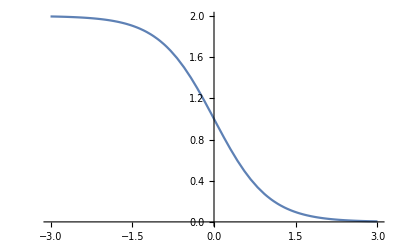

```mathematica
Plot[1-Tanh[x],{x,-3,3}]
```

```mathematica
T^4 Sum[Subscript[c, i](μB/T)^(2i),{i,0,2}]//FullSimplify
```

T^4 c_0+T^2 μB^2 c_1+μB^4 c_2